# Wolfram Mathematica: Introducción Rápida

## Introducción

Wolfram Mathematica es un sistema de softwarem matemático diseñado para realizar una amplia variedad de cálculos matemáticos, análisis y visualizaciones. Es conocido por su versatilidad en términos de manipulación matemática, resolución de ecuaciones, gráficos y visualización de datos, así como por su capacidad para abordar problemas en diversas áreas de la ciencia, la ingeniería, la computación y más.

Una característica distintiva de Mathematica es su lenguaje de programación integrado, llamado Wolfram Language. Este lenguaje permite a los usuarios expresar conceptos matemáticos y algorítmicos en un formato natural, lo que facilita la creación de programas y scripts para realizar cálculos complejos y automatizar tareas.

## Estructura Interna

Está dispuesto en dos partes fundamentales: El Kernel (motor de cálculo ) y el Front End (Interfaz de comunicación con el usuario). Cuando se comienza a utilizar el programa se activa el Front End con lo que se puede comenzar a introducir datos y expresiones. En el momento en que se desea realizar la primera operación se activa el Kernel que es el módulo que realiza el cálculo. 

Es importante mencionar que en lugar de recordar todos los comandos, hay botones con imágenes que hacen las cosas más fáciles. 

Todas estas características permiten un manejo sencillo y rápido de modo que, con una pequeña introducción a las funciones básicas, al modo de introducir datos y la utilización de la ayuda, se puede manejar con soltura en un corto espacio de tiempo.

## Operaciones Básicas

Empezar a trabajar con Mathematica es muy fácil!, sólo debemos ingresar la operación que se desea realizar y pulsar las teclas Shift + Intro.

Las operacones básicas son:

2 + 2 	adición

3 - 2		sustracción

2 * 5 		multiplicación

6 / 2		división

3 ^ 2		potencias

Observaciones Útiles

#### Observación 1

Mathemática intenta siempre llegar al resultado más aproximado en cada operacion que hace y siempre que puede llega al resultado exacto. Es por esto que cada vez que realiza una división, si el resultado no es un entero o no puede simplificarlo, entrega el resultado expresado como una fracción

```mathematica
15/4
```

```mathematica
(a^3 +1)/a
```

Ahora, para obtener el resultado aproximado o en forma decimal, existen tres formas de obtenerlo

a) Ingresar uno de los números en la operación que quieras hacer usando números decimales, por ejemplo usar 15. en lugar de 15.

Ejemplo:

```mathematica
15./4
```

b) Utilizar el comando N[ ], que permite obtener el resultado en forma decimal.

Ejemplo:

```mathematica
N[15/4]
```

```mathematica
N[15/4,1]
```

```mathematica
N[π,100]
```

c) Utilizar el comando N, pero al final de la expresión

Ejemplo:

```mathematica
15/4 //N
```

#### Observación 2

El resultado de la última operación se puede recuperar con %k

Ejemplo: %2 entrega el penúltimo resultado

```mathematica
2*5
```

10

```mathematica
30/ %2
```

3

## Comandos y Variables

Mathematica incorpora tanto sus propios comandos como algunas variables de uso muy frecuente de modo que la primera letra es siempre mayúscula. Algunas variables son

```mathematica
Pi //N
E //N
I
```

Ahora, en cuanto a los comandos, estos también comienzan siempre con una mayúscula, y el argumento que ocupamos para dicha variable siempre va entre corchetes.

```mathematica
Cos[Pi]
Max[1,5,10,17] 
RandomInteger[50]
Mean[{2,2,10}]//N
```

Hay más de 5000 funciones en el lenguaje de Wolfram, y podemos notar que cada vez que comenzamos a escribir una función, nos aparecerán sugerencias de funciones.

Algo que también es muy útil de saber es que en la sugerencia, aparece un símbolo de información ⓘ . Si hacemos click sobre él, se abrirá una ventana que entrega información sobre la función, ejemplos y funciones similares. Además, también se encuentra un buscador el que permite hallar funciones útiles para nosotros!

## Listas

En muchas ocasiones es necesario utilizar datos que se encuentran relacionados entre sí y que pueden ser todos ellos el argumento de una función. En esas ocasiones utilizamos listas para definir todos estos elementos.

Una lista contiene elementos que se encuentran separados por comas de la siguiente manera:

```mathematica
a={1, 3, 5, 7}
```

Y así podemos ocupar todos estos elementos como una sola variable, y aplicar funciones sobre ellas.

```mathematica
3*a
Cos[a]//N
ListLinePlot[a]
Table[a,2]//MatrixForm
```

## Definición de Funciones

Además de las funciones que podemos encontrar en Mathematica, también podemos definir nosotros mismos funciones a nuestra conveniencia.

Para definir funciones, éstas deben tener nombres o letras distintas a las variables o comandos  propios de Mathematica, y se realiza de la siguiente manera:

Nombre_de_la_Función[argumento/s_] : = función

Ejemplo:

```mathematica
f[x_]:= x^2 + 2*x
f[2]
f[5]
f[y]
```

```mathematica
?f
```

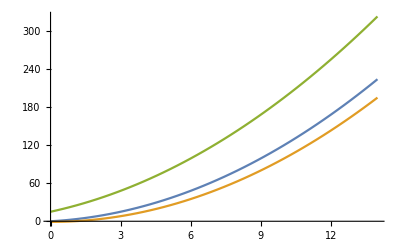

```mathematica
Plot[{f[x],f[x-1],f[x+3]},{x,0,14}]
```

También se pueden asignar valores a las variables de las funciones a través de la expresión /.

```mathematica
f[x]/.x->2
```

Lo que se entiende en palabras como: “Calcula cuánto vale f[x] tal que x = 2” .

Es importante mencionar que también podemos definir funciones por tramos, por ejemplo,

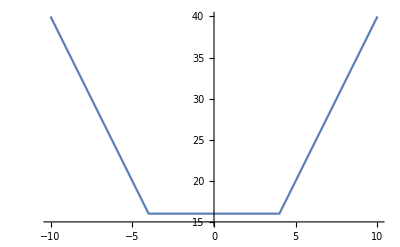

```mathematica
g[x_/;x<−1]:=−2x;
g[x_/;-1<=x<=1]:=2;
g[x_/;x>1]:=2x;
Plot[g[x],{x,-10,10},PlotRange->{15,40}]
```

#### Observación 1

Para borrar una variable, podemos hacerlo de dos formas, por ejemplo

Forma 1

```mathematica
a=2; a
```

```mathematica
a=.; a
```

Forma 2

```mathematica
a = 2; f[x_]:= x^2 + 2*x; f[a]
```

```mathematica
Clear[a,f]; f[a]
```

## Definción Función Alternativa (#)

Existe una manera alternativa de definir funciones, que es utilizando el símbolo “#”.

```mathematica
h=#^2&
```

```mathematica
h[3]
h[{1,2,3}]
```

```mathematica
k = #1+#2^2 &
```

```mathematica
k[1,6]
```

## ¿Mathematica Interactivo?

Una función bastante interesante de Wolfram Mathematica es la función Manipulate, función que permite construir interfaces para que el usuario pueda manipular variables de manera continua. La función Manipulate trabaja de modo parecido aTable, con la diferencia de que en lugar de producirse una lista de resultados, aparece un control deslizante con el que se puede elegir interactivamente el valor deseado.

```mathematica
?Manipulate
```

Veamos algunos ejemplos.

Ejemplo 1:

```mathematica
Manipulate[Table["Hola",n],{n,1,5,1}]
```

Ejemplo 2:

```mathematica
Manipulate[Column[{n,n+1,n+2}],{n,1,15,1}]
```

Ejemplo 3:

```mathematica
Manipulate[BarChart[{1,a,4,2*a,4,3*a,1},ChartStyle->"DarkRainbow"],{a,0,2}]
```

Ejemplo 4:

```mathematica
Manipulate[PieChart[{1,a,2*a,3*a,4},ChartStyle->"Pastel"],{a,0,5}]
```

Ejemplo 5:

```mathematica
Manipulate[Graphics[Style[RegularPolygon[n],Purple]],{n,5,10,1}]
```

Ejemplo 6:

```mathematica
g[x_,n_]=Sin[x^n];
Manipulate[Plot[{g[x],g[x,nn]},{x,0,π}],{nn,1.1,4.1,.1}]
```

## Estadística & Wolfram Mathematica

Wolfram Mathematica es un programa increíblemente útil cuando se trata de estadísticas y probabilidades, pues nos puede ayudar a analizar datos y calcular probabilidades, para hacer gráficos que muestren cómo los datos se distribuyen y para encontrar patrones en conjuntos de información. También puede resolver problemas de probabilidad, como lanzar dados o elegir cartas de una baraja.

Ejemplo 1: Calcule la probabilidad de que al lanzar 2 dados, uno de los dados sea 5 y el otro entregue un número menor a 5.

```mathematica
Probability[(x==5&&y<5)||(y==5&&x<5),{x\[Distributed]DiscreteUniformDistribution[{1,6}],y\[Distributed]DiscreteUniformDistribution[{1,6}]}]
```

2/9

Sabemos que la probabildad de obtener un 5 al tirar un dado es 1/5 y la probabilidad de obtener un número menor a 5 es 4/6, por lo tanto, la probabilidad es,

```mathematica
1/6* 4/6+4/6* 1/6
```

Para obtener el espacio muestral de este ejercicio, podemos utilizar la función Tuples, que entrega una lista de todas las posibles n-combinaciones de elementos de una lista. El espacio muestral al lanzar dos dados es,

```mathematica
Tuples[{1,2,3,4,5,6},2] (*El número 2 indica las veces que se lanzó el dado*)//Length
```

El espacio muestral al lanzar dos dados y obtener un 5 y un número menor a 5 es,

```mathematica
Select[Tuples[{1,2,3,4,5,6},2],(#[[1]]==5&&#[[2]]<5 )||(#[[2]]==5&&#[[1]]<5 ) &]
```

Explicación: Los símbolos “[[  ]]” en Wolfram Mathematica son utilizados para acceder a elementos específicos en una lista, matriz o cualquier otra estructura. En el ejemplo, “#[[1]]” y “#[[2]]” se utilizan para acceder al primer y al segundo elemento respectivamente de un par (tupla) en una lista generada por la función Tuples.

También, es importante notar que se utiliza & para denotar que finalizamos la función.

Ejemplo 2 : Calcule la probabilidad de que al lanzar un dado dos veces, el primer resultado sea 5 y el otro segundo sea un número menor a 5.

```mathematica
Probability[(x==5&&y<5),{x\[Distributed]DiscreteUniformDistribution[{1,6}],y\[Distributed]DiscreteUniformDistribution[{1,6}]}]
```

Espacio muestral es,

```mathematica
Select[Tuples[{1,2,3,4,5,6},2],(#[[1]]==5&&#[[2]]<5 ) &]
```